```mathematica
Edges[list_]:=Block[
{l, result, chunk, colors =ColorData[1,"ColorList"],
assoc= EdgeCycleMat[ReadGrof[list[[1,1]]]], i},
result={};
result=Table[
With[
{record=Read[StringToStream[list[[i,3]]]]},
record[[2]]->Row[{ToString[ChromaticPolynomial[ReadGrof[list[[i,2]]],4]/24 ]<> " * " ,Style[ToString[Take[assoc[Sort[record[[2]]]],{3,5}]],FontSize->8]}] 
],{i,1,Length[list]}];
Return[result]
]
```

```mathematica
ComputeVertexLabels[g_]:=Block[
{assoc2= CycleMat[g], result, assoc,i},
assoc=Association[];
For[i=1,i≤Length[assoc2],i++,
assoc[i]=assoc2[[i]]
];
result=Table[v->Row[{ToString[v]<>" * " , Style[ToString[Take[assoc[v],{3,5}]],FontSize->8]}],{v,VertexList[g]}];
Return[result]
]
```

```mathematica
ComputeVertexLabels[ReadGrof[383]]
```

{1→1 * {4, 11, 32},2→2 * {6, 18, 52},3→3 * {9, 28, 83},7→7 * {4, 12, 36},11→11 * {4, 11, 32},5→5 * {10, 33, 93},9→9 * {6, 18, 58},6→6 * {5, 16, 50},8→8 * {4, 12, 40},4→4 * {4, 10, 33},10→10 * {4, 11, 36}}

```mathematica
Edges[values383]
```

StringJoin::string: String expected at position 1 in Bold[25] <> " * ".

StringJoin::string: String expected at position 1 in Bold[17] <> " * ".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

{1<->7→Bold[25]<> * {2, 5, 14},3<->7→Bold[25]<> * {2, 7, 22},3<->5→Bold[17]<> * {4, 13, 28},3<->8→Bold[48]<> * {2, 6, 23},5<->8→Bold[12]<> * {2, 8, 24},4<->5→Bold[12]<> * {2, 6, 20},3<->6→Bold[12]<> * {2, 7, 25},2<->9→Bold[20]<> * {2, 6, 22},3<->9→Bold[36]<> * {3, 8, 26},2<->5→Bold[15]<> * {3, 9, 25},5<->9→Bold[24]<> * {3, 10, 27},5<->10→Bold[12]<> * {2, 7, 21},1<->11→Bold[25]<> * {2, 5, 14},5<->7→Bold[25]<> * {2, 7, 22},4<->8→Bold[48]<> * {2, 4, 15},6<->8→Bold[12]<> * {2, 6, 18},4<->6→Bold[12]<> * {2, 6, 17},6<->9→Bold[12]<> * {2, 7, 22},4<->10→Bold[48]<> * {2, 4, 14},6<->10→Bold[12]<> * {2, 6, 18},9<->10→Bold[48]<> * {2, 5, 19},2<->11→Bold[25]<> * {2, 6, 17},7<->11→Bold[25]<> * {2, 5, 14},5<->11→Bold[25]<> * {2, 6, 19}}

```mathematica
values383={{383,2601,"{2,1<->7,3<->11}"},
{383,3044,"{2,3<->7,1<->5}"},
{383,2489,"{2,3<->5,7<->8}"},
{383,3045,"{2,3<->8,5<->6}"},
{383,3046,"{2,5<->8,3<->4}"},
{383,1640,"{2,4<->5,8<->10}"},
{383,3047,"{2,3<->6,8<->9}"},
{383,2467,"{2,2<->9,3<->5}"},
{383,3048,"{2,3<->9,2<->6}"},
{383,3049,"{2,2<->5,9<->11}"},
{383,3050,"{2,5<->9,2<->10}"},
{383,3051,"{2,5<->10,4<->9}"},
{383,1827,"{2,1<->11,2<->7}"},
{383,2601,"{2,5<->7,3<->11}"},
{383,3045,"{2,4<->8,5<->6}"},
{383,3046,"{2,6<->8,3<->4}"},
{383,1640,"{2,4<->6,8<->10}"},
{383,3046,"{2,6<->9,3<->10}"},
{383,3045,"{2,4<->10,5<->6}"},
{383,3051,"{2,6<->10,4<->9}"},
{383,3045,"{2,9<->10,5<->6}"},
{383,3044,"{2,2<->11,1<->5}"},
{383,3044,"{2,7<->11,1<->5}"},
{383,1827,"{2,5<->11,2<->7}"}
}
```

{{383,2601,{2,1<->7,3<->11}},{383,3044,{2,3<->7,1<->5}},{383,2489,{2,3<->5,7<->8}},{383,3045,{2,3<->8,5<->6}},{383,3046,{2,5<->8,3<->4}},{383,1640,{2,4<->5,8<->10}},{383,3047,{2,3<->6,8<->9}},{383,2467,{2,2<->9,3<->5}},{383,3048,{2,3<->9,2<->6}},{383,3049,{2,2<->5,9<->11}},{383,3050,{2,5<->9,2<->10}},{383,3051,{2,5<->10,4<->9}},{383,1827,{2,1<->11,2<->7}},{383,2601,{2,5<->7,3<->11}},{383,3045,{2,4<->8,5<->6}},{383,3046,{2,6<->8,3<->4}},{383,1640,{2,4<->6,8<->10}},{383,3046,{2,6<->9,3<->10}},{383,3045,{2,4<->10,5<->6}},{383,3051,{2,6<->10,4<->9}},{383,3045,{2,9<->10,5<->6}},{383,3044,{2,2<->11,1<->5}},{383,3044,{2,7<->11,1<->5}},{383,1827,{2,5<->11,2<->7}}}

```mathematica
Chrom[383]/24
```

20

```mathematica
Transf[values383,20]
```

{Style[{1<->7,3<->11},Automatic,Thickness[Large],RGBColor[0.6, 0.42664098839727194, 0.24]],Style[{3<->7,1<->5},Automatic,Thickness[Large],RGBColor[0.6, 0.24, 0.2941043604063603]],{3<->5,7<->8},Style[{3<->8,5<->6},Automatic,Thickness[Large],RGBColor[0.24720000000000014, 0.24, 0.6]],{5<->8,3<->4},{4<->5,8<->10},{3<->6,8<->9},{2<->9,3<->5},Style[{3<->9,2<->6},Automatic,Thickness[Large],RGBColor[0.24, 0.6, 0.33692049419863584]],{2<->5,9<->11},Style[{5<->9,2<->10},Automatic,Thickness[Large],RGBColor[0.6, 0.24, 0.5632658430022722]],{5<->10,4<->9},Style[{1<->11,2<->7},Automatic,Thickness[Large],RGBColor[0.24, 0.5939180232054561, 0.6]],Style[{5<->7,3<->11},Automatic,Thickness[Large],RGBColor[0.6, 0.42664098839727194, 0.24]],Style[{4<->8,5<->6},Automatic,Thickness[Large],RGBColor[0.24720000000000014, 0.24, 0.6]],{6<->8,3<->4},{4<->6,8<->10},{6<->9,3<->10},Style[{4<->10,5<->6},Automatic,Thickness[Large],RGBColor[0.24720000000000014, 0.24, 0.6]],{6<->10,4<->9},Style[{9<->10,5<->6},Automatic,Thickness[Large],RGBColor[0.24720000000000014, 0.24, 0.6]],Style[{2<->11,1<->5},Automatic,Thickness[Large],RGBColor[0.6, 0.24, 0.2941043604063603]],Style[{7<->11,1<->5},Automatic,Thickness[Large],RGBColor[0.6, 0.24, 0.2941043604063603]],Style[{5<->11,2<->7},Automatic,Thickness[Large],RGBColor[0.24, 0.5939180232054561, 0.6]]}

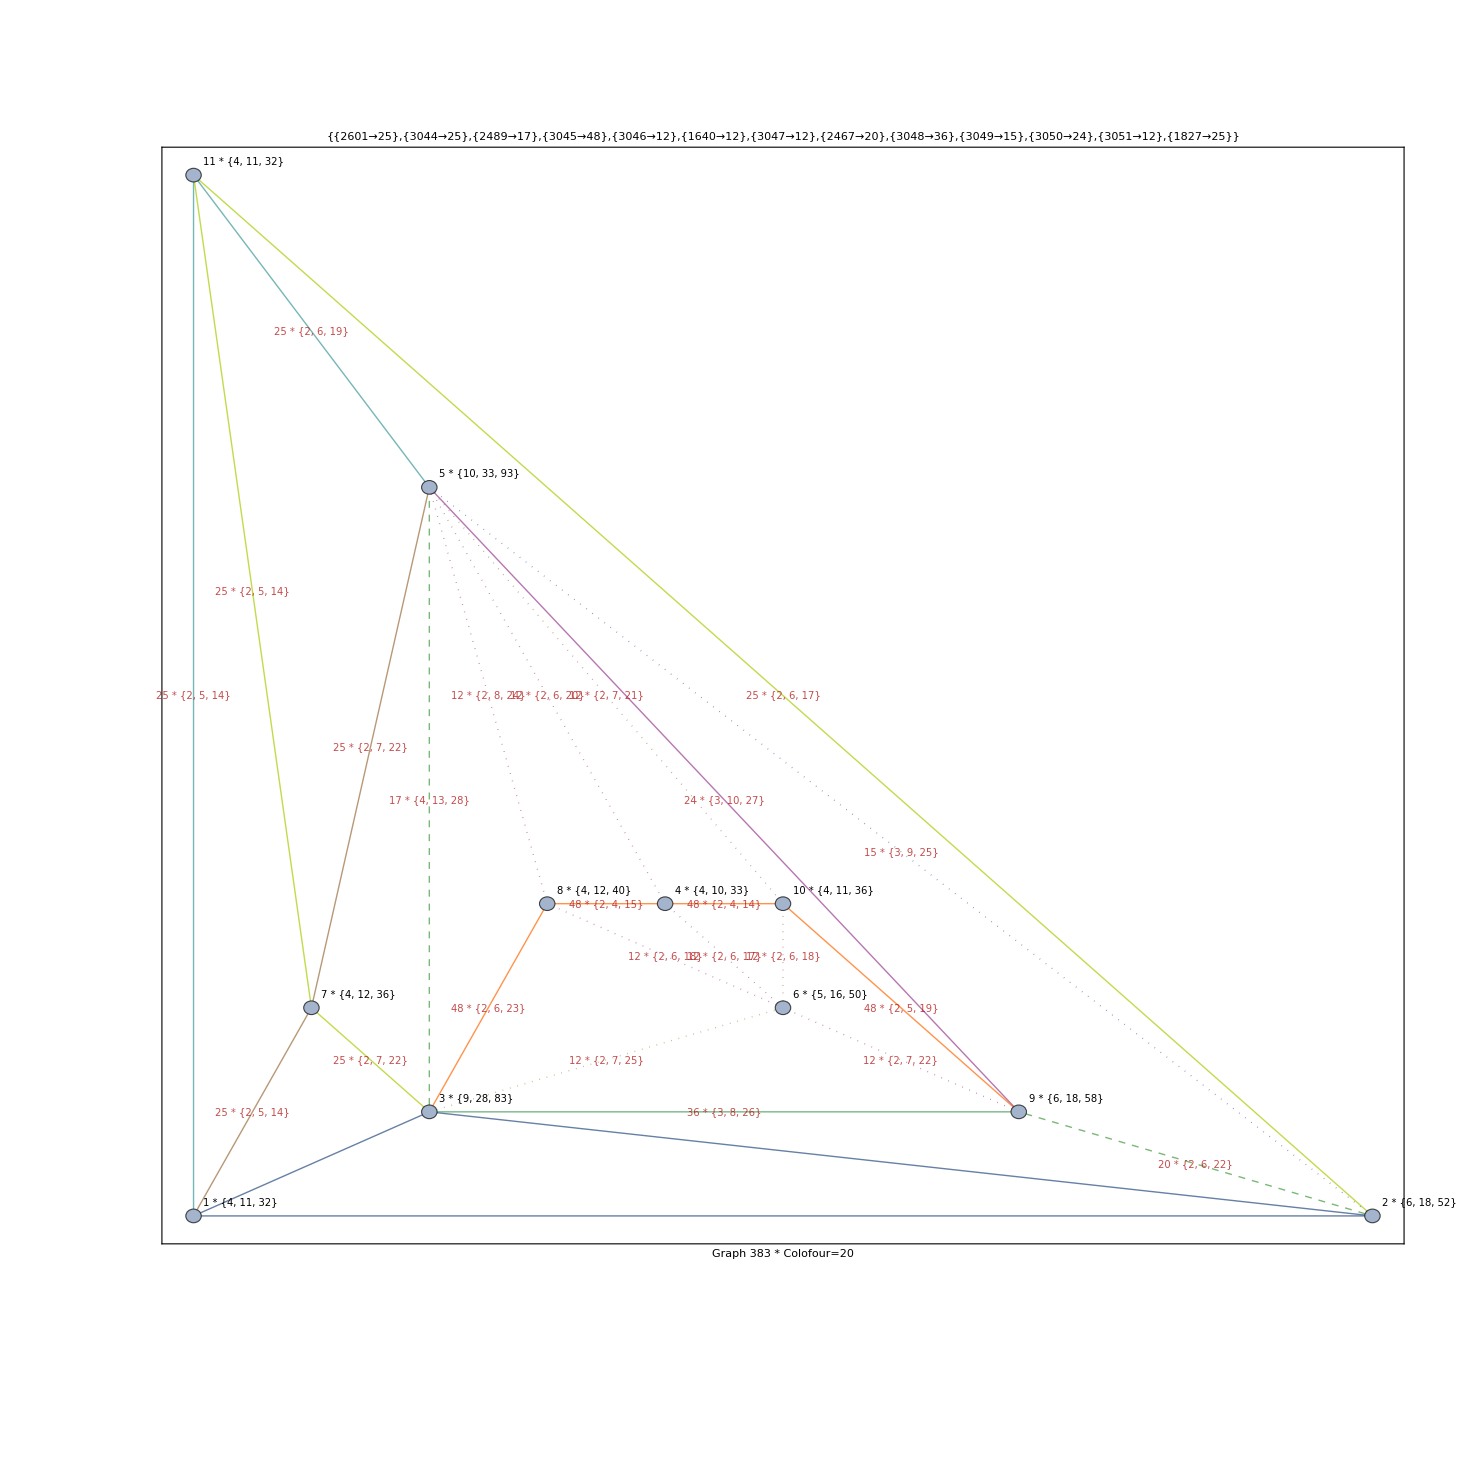

```mathematica
With[
{gn=383, val=values383},
With[
{g=ReadGrof[gn]},
HighlightGraph[Graph[g,VertexLabels->ComputeVertexLabels[g],VertexLabelStyle->Directive[Black,10], EdgeLabelStyle->Directive[Darker[Red],Italic,10],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], PlotLabel->Title[val],LabelStyle->Directive[8], ImageSize->800,EdgeLabels->Edges[val]],Join[
Transf[val,Chrom[gn]/24],
ReadGraphDiamondHighLights[gn]
]]
]
]
```

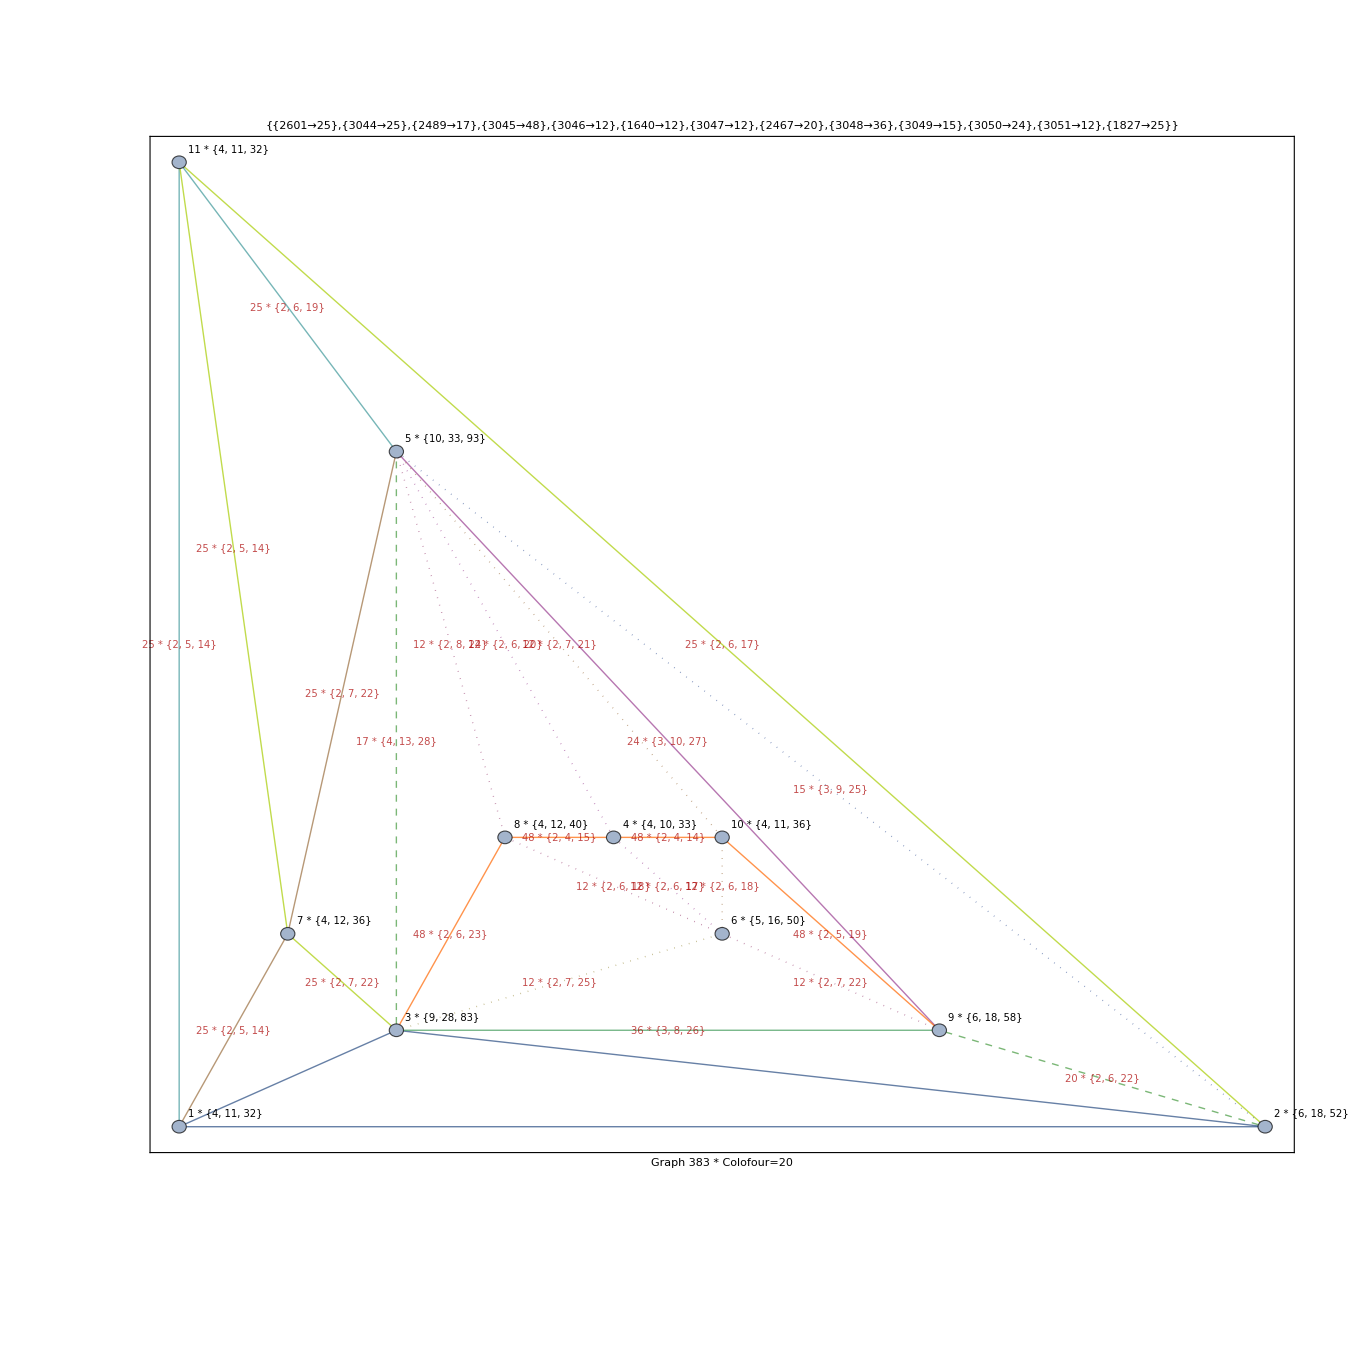

```mathematica
With[
{gn=383, val=values383},
With[
{g=ReadGrof[gn]},
HighlightGraph[Graph[g,VertexLabels->ComputeVertexLabels[g],VertexLabelStyle->Directive[Black,10], EdgeLabelStyle->Directive[Darker[Red],Italic,10],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], PlotLabel->Title[val],LabelStyle->Directive[8], ImageSize->800,EdgeLabels->Edges[val]],Join[
Transf[val,Chrom[gn]/24],
ReadGraphDiamondHighLights[gn]
]]
]
]
```

```mathematica
VertexCycleVect[g_, vertex1_, vertex2_]:=Block[
{cycles,vertexCount=VertexCount[g],result,result2, k,l,m, current,currentLength},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[0,{i,1,vertexCount}];
result2=Table[{},{i,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
If[(MemberQ[current,vertex1<->_])&&(MemberQ[current,vertex2<->_]),
currentLength=Length[current];
result[[currentLength]]++;
AppendTo[result2[[currentLength]],current];
]
];
result
]
```

```mathematica
If[(MemberQ[current,vertex1<->_]||MemberQ[current,_<->vertex1])&&(MemberQ[current,vertex2<->_]||MemberQ[current,_<->vertex2]),
currentLength=Length[current];
result[[currentLength]]++;
AppendTo[result2[[currentLength]],current];
]
```

```mathematica
VertexCycleVect[ReadGrof[7],1,5]
```

{0,0,2,7,22,37,30}

```mathematica
VertexCycleVect[ReadGrof[7],2,7]
```

{0,0,0,3,15,34,30}

```mathematica
VertexCycleVect[ReadGrof[7],7,4]
```

{0,0,2,5,17,34,30}

```mathematica
VertexCycleVect[ReadGrof[7],3,5]
```

{0,0,0,10,30,40,30}

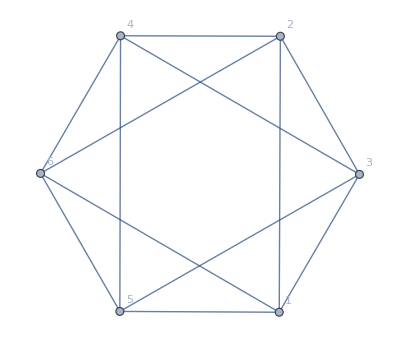

```mathematica
Graph[ReadGrof[4],VertexLabels->"Name"]
```

```mathematica
FindCycle[{ReadGrof[4],4},{1,10},All]
```

{{4<->3,3<->5,5<->4},{4<->3,3<->2,2<->4},{4<->2,2<->6,6<->4},{4<->5,5<->6,6<->4},{4<->3,3<->1,1<->5,5<->4},{4<->5,5<->6,6<->2,2<->4},{4<->5,5<->3,3<->2,2<->4},{4<->5,5<->1,1<->2,2<->4},{4<->3,3<->1,1<->2,2<->4},{4<->2,2<->1,1<->6,6<->4},{4<->3,3<->1,1<->6,6<->4},{4<->3,3<->2,2<->6,6<->4},{4<->3,3<->5,5<->6,6<->4},{4<->5,5<->1,1<->6,6<->4},{4<->3,3<->2,2<->1,1<->5,5<->4},{4<->3,3<->2,2<->6,6<->5,5<->4},{4<->3,3<->1,1<->6,6<->5,5<->4},{4<->5,5<->6,6<->1,1<->2,2<->4},{4<->5,5<->3,3<->1,1<->2,2<->4},{4<->5,5<->1,1<->6,6<->2,2<->4},{4<->5,5<->1,1<->3,3<->2,2<->4},{4<->3,3<->5,5<->6,6<->2,2<->4},{4<->3,3<->5,5<->1,1<->2,2<->4},{4<->3,3<->1,1<->6,6<->2,2<->4},{4<->2,2<->1,1<->5,5<->6,6<->4},{4<->2,2<->3,3<->1,1<->6,6<->4},{4<->2,2<->3,3<->5,5<->6,6<->4},{4<->3,3<->1,1<->2,2<->6,6<->4},{4<->3,3<->1,1<->5,5<->6,6<->4},{4<->3,3<->2,2<->1,1<->6,6<->4},{4<->3,3<->5,5<->1,1<->6,6<->4},{4<->5,5<->1,1<->2,2<->6,6<->4},{4<->5,5<->3,3<->1,1<->6,6<->4},{4<->5,5<->3,3<->2,2<->6,6<->4},{4<->3,3<->2,2<->1,1<->6,6<->5,5<->4},{4<->3,3<->2,2<->6,6<->1,1<->5,5<->4},{4<->3,3<->1,1<->2,2<->6,6<->5,5<->4},{4<->5,5<->6,6<->1,1<->3,3<->2,2<->4},{4<->5,5<->3,3<->1,1<->6,6<->2,2<->4},{4<->3,3<->5,5<->6,6<->1,1<->2,2<->4},{4<->3,3<->5,5<->1,1<->6,6<->2,2<->4},{4<->3,3<->1,1<->5,5<->6,6<->2,2<->4},{4<->2,2<->1,1<->3,3<->5,5<->6,6<->4},{4<->2,2<->3,3<->1,1<->5,5<->6,6<->4},{4<->2,2<->3,3<->5,5<->1,1<->6,6<->4},{4<->3,3<->2,2<->1,1<->5,5<->6,6<->4},{4<->3,3<->5,5<->1,1<->2,2<->6,6<->4},{4<->5,5<->1,1<->3,3<->2,2<->6,6<->4},{4<->5,5<->3,3<->1,1<->2,2<->6,6<->4},{4<->5,5<->3,3<->2,2<->1,1<->6,6<->4}}

```mathematica
values7={{7,18,"{2,1<->5,2<->7}"},
{7,21,"{2,2<->6,3<->5}"},
{7,18,"{2,2<->5,1<->6}"},
{7,18,"{2,3<->6,2<->4}"},
{7,18,"{2,3<->4,6<->7}"},
{7,21,"{2,4<->6,3<->5}"},
{7,18,"{2,5<->6,2<->4}"},
{7,18,"{2,4<->5,6<->7}"},
{7,21,"{2,1<->7,3<->5}"},
{7,18,"{2,3<->7,1<->4}"},
{7,18,"{2,5<->7,1<->4}"},
{7,21,"{2,4<->7,3<->5}"}


}
```

{{7,18,{2,1<->5,2<->7}},{7,21,{2,2<->6,3<->5}},{7,18,{2,2<->5,1<->6}},{7,18,{2,3<->6,2<->4}},{7,18,{2,3<->4,6<->7}},{7,21,{2,4<->6,3<->5}},{7,18,{2,5<->6,2<->4}},{7,18,{2,4<->5,6<->7}},{7,21,{2,1<->7,3<->5}},{7,18,{2,3<->7,1<->4}},{7,18,{2,5<->7,1<->4}},{7,21,{2,4<->7,3<->5}}}

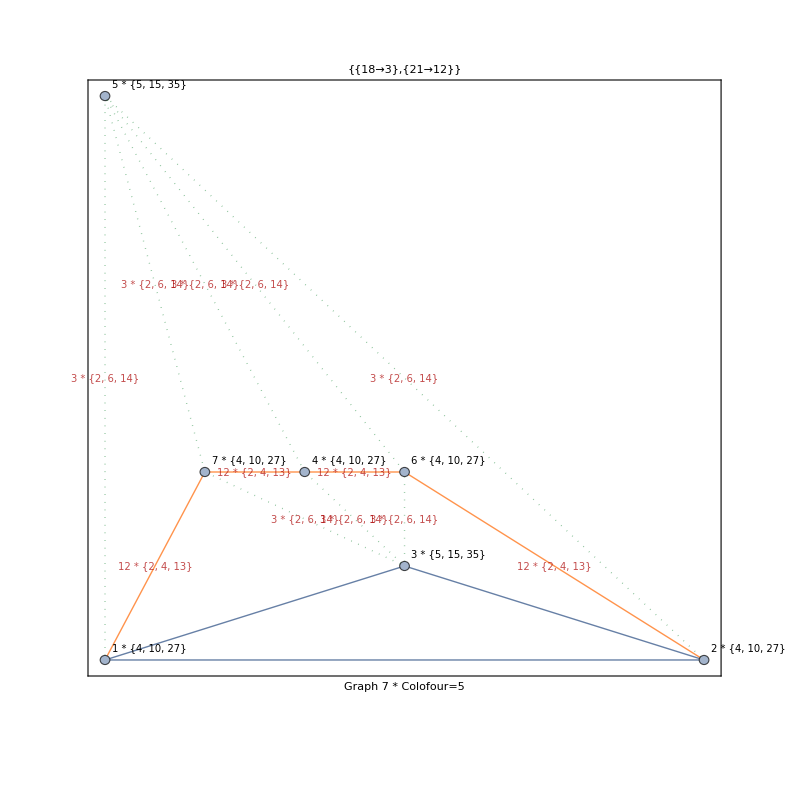

```mathematica
With[
{gn=7, val=values7},
With[
{g=ReadGrof[gn]},
HighlightGraph[Graph[g,VertexLabels->ComputeVertexLabels[g],VertexLabelStyle->Directive[Black,10], EdgeLabelStyle->Directive[Darker[Red],Italic,10],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], PlotLabel->Title[val],LabelStyle->Directive[8], ImageSize->800,EdgeLabels->Edges[val]],Join[
Transf[val,Chrom[gn]/24],
ReadGraphDiamondHighLights[gn]
]]
]
]
```

```mathematica
ModVertexCycleVect[g_, vertex1_, vertex2_]:=Block[
{cycles,vertexCount=VertexCount[g],result,result2, k,l,m, current,currentLength},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[0,{i,1,vertexCount}];
result2=Table[{},{i,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
If[(MemberQ[current,vertex1<->_])&&(MemberQ[current,vertex2<->_]),
currentLength=Length[current];
result[[currentLength]]=Mod[result[[currentLength]]+1, currentLength];
AppendTo[result2[[currentLength]],current];
]
];
result
]
```

```mathematica
MyShort[g_,v_]:=v->VertexCycleVect2[g,v]
```

```mathematica
EvenOdd[list_]:=Block[{result,i},
result={0,0};
For[i=1,i≤Length[list],i++,
result[[If[EvenQ[i],1,2]]]+=list[[i]]
];
result
]
```

```mathematica
EvenOdd[{1,2,3}]
```

{2,4}

```mathematica
ModExplainRule2WithCycles[list_]:=Block[
{l, result, chunk, colors =ColorData[1,"ColorList"],
 i},
result={};
result=Table[
With[
{record=Read[StringToStream[list[[i,3]]]]},
With[
{g=ReadGrof[list[[i,1]]],g2=ReadGrof[list[[i,2]]]},
{(Chrom[list[[i,2]]]/24)-(Chrom[list[[i,1]]]/24),
list[[i,1]]->(Chrom[list[[i,1]]]/24),record[[2]],
list[[i,2]]->(Chrom[list[[i,2]]]/24),record[[3]],
Table[
MyShort[g,s],{s,Subsets[{record[[2,1]],record[[2,2]],record[[3,1]],record[[3,2]]}]}],
Table[
MyShort[g2,s],{s,Subsets[{record[[2,1]],record[[2,2]],record[[3,1]],record[[3,2]]}]}]
} 
]
],{i,1,Length[list]}];
Return[Sort[result]]
]
```

```mathematica
Grid[ModExplainRule2WithCycles[values7], Frame->All]
```

-2 | 7→5 | 1<->5 | 18→3 | 2<->7 | {{}→{0,0,10,20,41,50,30},{1}→{0,0,4,10,27,42,30},{5}→{0,0,5,15,35,45,30},{2}→{0,0,4,10,27,42,30},{7}→{0,0,4,10,27,42,30},{1,5}→{0,0,2,7,22,37,30},{1,2}→{0,0,2,5,17,34,30},{1,7}→{0,0,2,5,17,34,30},{5,2}→{0,0,2,7,22,37,30},{5,7}→{0,0,2,7,22,37,30},{2,7}→{0,0,0,3,15,34,30},{1,5,2}→{0,0,1,3,13,29,30},{1,5,7}→{0,0,1,3,13,29,30},{1,2,7}→{0,0,0,2,9,26,30},{5,2,7}→{0,0,0,2,11,29,30},{1,5,2,7}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{1}→{0,0,4,9,29,68,94,60},{5}→{0,0,5,14,41,82,102,60},{2}→{0,0,5,14,41,82,102,60},{7}→{0,0,4,9,29,68,94,60},{1,5}→{0,0,0,3,18,53,84,60},{1,2}→{0,0,2,6,21,53,84,60},{1,7}→{0,0,2,5,16,44,76,60},{5,2}→{0,0,2,8,28,65,92,60},{5,7}→{0,0,2,5,20,55,84,60},{2,7}→{0,0,2,6,21,53,84,60},{1,5,2}→{0,0,0,2,12,39,74,60},{1,5,7}→{0,0,0,2,10,34,66,60},{1,2,7}→{0,0,1,3,11,32,66,60},{5,2,7}→{0,0,1,3,13,41,74,60},{1,5,2,7}→{0,0,0,1,6,23,56,60}}
-2 | 7→5 | 2<->5 | 18→3 | 1<->6 | {{}→{0,0,10,20,41,50,30},{2}→{0,0,4,10,27,42,30},{5}→{0,0,5,15,35,45,30},{1}→{0,0,4,10,27,42,30},{6}→{0,0,4,10,27,42,30},{2,5}→{0,0,2,7,22,37,30},{2,1}→{0,0,2,5,17,34,30},{2,6}→{0,0,2,5,17,34,30},{5,1}→{0,0,2,7,22,37,30},{5,6}→{0,0,2,7,22,37,30},{1,6}→{0,0,0,3,15,34,30},{2,5,1}→{0,0,1,3,13,29,30},{2,5,6}→{0,0,1,3,13,29,30},{2,1,6}→{0,0,0,2,9,26,30},{5,1,6}→{0,0,0,2,11,29,30},{2,5,1,6}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{2}→{0,0,5,14,41,82,102,60},{5}→{0,0,5,14,41,82,102,60},{1}→{0,0,4,9,29,68,94,60},{6}→{0,0,4,9,29,68,94,60},{2,5}→{0,0,2,8,28,65,92,60},{2,1}→{0,0,2,6,21,53,84,60},{2,6}→{0,0,2,5,20,55,84,60},{5,1}→{0,0,0,3,18,53,84,60},{5,6}→{0,0,2,6,21,53,84,60},{1,6}→{0,0,0,1,10,41,76,60},{2,5,1}→{0,0,0,2,12,39,74,60},{2,5,6}→{0,0,1,3,13,41,74,60},{2,1,6}→{0,0,0,1,7,31,66,60},{5,1,6}→{0,0,0,0,5,29,66,60},{2,5,1,6}→{0,0,0,0,3,20,56,60}}
-2 | 7→5 | 3<->4 | 18→3 | 6<->7 | {{}→{0,0,10,20,41,50,30},{3}→{0,0,5,15,35,45,30},{4}→{0,0,4,10,27,42,30},{6}→{0,0,4,10,27,42,30},{7}→{0,0,4,10,27,42,30},{3,4}→{0,0,2,7,22,37,30},{3,6}→{0,0,2,7,22,37,30},{3,7}→{0,0,2,7,22,37,30},{4,6}→{0,0,2,5,17,34,30},{4,7}→{0,0,2,5,17,34,30},{6,7}→{0,0,0,3,15,34,30},{3,4,6}→{0,0,1,3,13,29,30},{3,4,7}→{0,0,1,3,13,29,30},{3,6,7}→{0,0,0,2,11,29,30},{4,6,7}→{0,0,0,2,9,26,30},{3,4,6,7}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{3}→{0,0,5,14,41,82,102,60},{4}→{0,0,4,9,29,68,94,60},{6}→{0,0,4,9,29,68,94,60},{7}→{0,0,4,9,29,68,94,60},{3,4}→{0,0,2,6,21,53,84,60},{3,6}→{0,0,2,6,21,53,84,60},{3,7}→{0,0,0,3,18,53,84,60},{4,6}→{0,0,2,5,16,44,76,60},{4,7}→{0,0,0,1,10,41,76,60},{6,7}→{0,0,0,1,10,41,76,60},{3,4,6}→{0,0,1,3,11,32,66,60},{3,4,7}→{0,0,0,0,5,29,66,60},{3,6,7}→{0,0,0,0,5,29,66,60},{4,6,7}→{0,0,0,0,3,22,58,60},{3,4,6,7}→{0,0,0,0,0,13,48,60}}
-2 | 7→5 | 3<->6 | 18→3 | 2<->4 | {{}→{0,0,10,20,41,50,30},{3}→{0,0,5,15,35,45,30},{6}→{0,0,4,10,27,42,30},{2}→{0,0,4,10,27,42,30},{4}→{0,0,4,10,27,42,30},{3,6}→{0,0,2,7,22,37,30},{3,2}→{0,0,2,7,22,37,30},{3,4}→{0,0,2,7,22,37,30},{6,2}→{0,0,2,5,17,34,30},{6,4}→{0,0,2,5,17,34,30},{2,4}→{0,0,0,3,15,34,30},{3,6,2}→{0,0,1,3,13,29,30},{3,6,4}→{0,0,1,3,13,29,30},{3,2,4}→{0,0,0,2,11,29,30},{6,2,4}→{0,0,0,2,9,26,30},{3,6,2,4}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{3}→{0,0,5,14,41,82,102,60},{6}→{0,0,4,9,29,68,94,60},{2}→{0,0,5,14,41,82,102,60},{4}→{0,0,4,9,29,68,94,60},{3,6}→{0,0,2,6,21,53,84,60},{3,2}→{0,0,2,8,28,65,92,60},{3,4}→{0,0,2,6,21,53,84,60},{6,2}→{0,0,2,5,20,55,84,60},{6,4}→{0,0,2,5,16,44,76,60},{2,4}→{0,0,0,3,18,53,84,60},{3,6,2}→{0,0,1,3,13,41,74,60},{3,6,4}→{0,0,1,3,11,32,66,60},{3,2,4}→{0,0,0,2,12,39,74,60},{6,2,4}→{0,0,0,2,10,34,66,60},{3,6,2,4}→{0,0,0,1,6,23,56,60}}
-2 | 7→5 | 3<->7 | 18→3 | 1<->4 | {{}→{0,0,10,20,41,50,30},{3}→{0,0,5,15,35,45,30},{7}→{0,0,4,10,27,42,30},{1}→{0,0,4,10,27,42,30},{4}→{0,0,4,10,27,42,30},{3,7}→{0,0,2,7,22,37,30},{3,1}→{0,0,2,7,22,37,30},{3,4}→{0,0,2,7,22,37,30},{7,1}→{0,0,2,5,17,34,30},{7,4}→{0,0,2,5,17,34,30},{1,4}→{0,0,0,3,15,34,30},{3,7,1}→{0,0,1,3,13,29,30},{3,7,4}→{0,0,1,3,13,29,30},{3,1,4}→{0,0,0,2,11,29,30},{7,1,4}→{0,0,0,2,9,26,30},{3,7,1,4}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{3}→{0,0,5,14,41,82,102,60},{7}→{0,0,4,9,29,68,94,60},{1}→{0,0,4,9,29,68,94,60},{4}→{0,0,4,9,29,68,94,60},{3,7}→{0,0,0,3,18,53,84,60},{3,1}→{0,0,2,5,20,55,84,60},{3,4}→{0,0,2,6,21,53,84,60},{7,1}→{0,0,2,5,16,44,76,60},{7,4}→{0,0,0,1,10,41,76,60},{1,4}→{0,0,0,1,10,41,76,60},{3,7,1}→{0,0,0,2,10,34,66,60},{3,7,4}→{0,0,0,0,5,29,66,60},{3,1,4}→{0,0,0,1,7,31,66,60},{7,1,4}→{0,0,0,0,3,22,58,60},{3,7,1,4}→{0,0,0,0,2,15,48,60}}
-2 | 7→5 | 4<->5 | 18→3 | 6<->7 | {{}→{0,0,10,20,41,50,30},{4}→{0,0,4,10,27,42,30},{5}→{0,0,5,15,35,45,30},{6}→{0,0,4,10,27,42,30},{7}→{0,0,4,10,27,42,30},{4,5}→{0,0,2,7,22,37,30},{4,6}→{0,0,2,5,17,34,30},{4,7}→{0,0,2,5,17,34,30},{5,6}→{0,0,2,7,22,37,30},{5,7}→{0,0,2,7,22,37,30},{6,7}→{0,0,0,3,15,34,30},{4,5,6}→{0,0,1,3,13,29,30},{4,5,7}→{0,0,1,3,13,29,30},{4,6,7}→{0,0,0,2,9,26,30},{5,6,7}→{0,0,0,2,11,29,30},{4,5,6,7}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{4}→{0,0,4,9,29,68,94,60},{5}→{0,0,5,14,41,82,102,60},{6}→{0,0,4,9,29,68,94,60},{7}→{0,0,4,9,29,68,94,60},{4,5}→{0,0,2,6,21,53,84,60},{4,6}→{0,0,2,5,16,44,76,60},{4,7}→{0,0,0,1,10,41,76,60},{5,6}→{0,0,2,6,21,53,84,60},{5,7}→{0,0,2,5,20,55,84,60},{6,7}→{0,0,0,1,10,41,76,60},{4,5,6}→{0,0,1,3,11,32,66,60},{4,5,7}→{0,0,0,1,7,31,66,60},{4,6,7}→{0,0,0,0,3,22,58,60},{5,6,7}→{0,0,0,1,7,31,66,60},{4,5,6,7}→{0,0,0,0,2,15,48,60}}
-2 | 7→5 | 5<->6 | 18→3 | 2<->4 | {{}→{0,0,10,20,41,50,30},{5}→{0,0,5,15,35,45,30},{6}→{0,0,4,10,27,42,30},{2}→{0,0,4,10,27,42,30},{4}→{0,0,4,10,27,42,30},{5,6}→{0,0,2,7,22,37,30},{5,2}→{0,0,2,7,22,37,30},{5,4}→{0,0,2,7,22,37,30},{6,2}→{0,0,2,5,17,34,30},{6,4}→{0,0,2,5,17,34,30},{2,4}→{0,0,0,3,15,34,30},{5,6,2}→{0,0,1,3,13,29,30},{5,6,4}→{0,0,1,3,13,29,30},{5,2,4}→{0,0,0,2,11,29,30},{6,2,4}→{0,0,0,2,9,26,30},{5,6,2,4}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{5}→{0,0,5,14,41,82,102,60},{6}→{0,0,4,9,29,68,94,60},{2}→{0,0,5,14,41,82,102,60},{4}→{0,0,4,9,29,68,94,60},{5,6}→{0,0,2,6,21,53,84,60},{5,2}→{0,0,2,8,28,65,92,60},{5,4}→{0,0,2,6,21,53,84,60},{6,2}→{0,0,2,5,20,55,84,60},{6,4}→{0,0,2,5,16,44,76,60},{2,4}→{0,0,0,3,18,53,84,60},{5,6,2}→{0,0,1,3,13,41,74,60},{5,6,4}→{0,0,1,3,11,32,66,60},{5,2,4}→{0,0,0,2,12,39,74,60},{6,2,4}→{0,0,0,2,10,34,66,60},{5,6,2,4}→{0,0,0,1,6,23,56,60}}
-2 | 7→5 | 5<->7 | 18→3 | 1<->4 | {{}→{0,0,10,20,41,50,30},{5}→{0,0,5,15,35,45,30},{7}→{0,0,4,10,27,42,30},{1}→{0,0,4,10,27,42,30},{4}→{0,0,4,10,27,42,30},{5,7}→{0,0,2,7,22,37,30},{5,1}→{0,0,2,7,22,37,30},{5,4}→{0,0,2,7,22,37,30},{7,1}→{0,0,2,5,17,34,30},{7,4}→{0,0,2,5,17,34,30},{1,4}→{0,0,0,3,15,34,30},{5,7,1}→{0,0,1,3,13,29,30},{5,7,4}→{0,0,1,3,13,29,30},{5,1,4}→{0,0,0,2,11,29,30},{7,1,4}→{0,0,0,2,9,26,30},{5,7,1,4}→{0,0,0,1,6,21,30}} | {{}→{0,0,12,23,56,100,112,60},{5}→{0,0,5,14,41,82,102,60},{7}→{0,0,4,9,29,68,94,60},{1}→{0,0,4,9,29,68,94,60},{4}→{0,0,4,9,29,68,94,60},{5,7}→{0,0,2,5,20,55,84,60},{5,1}→{0,0,0,3,18,53,84,60},{5,4}→{0,0,2,6,21,53,84,60},{7,1}→{0,0,2,5,16,44,76,60},{7,4}→{0,0,0,1,10,41,76,60},{1,4}→{0,0,0,1,10,41,76,60},{5,7,1}→{0,0,0,2,10,34,66,60},{5,7,4}→{0,0,0,1,7,31,66,60},{5,1,4}→{0,0,0,0,5,29,66,60},{7,1,4}→{0,0,0,0,3,22,58,60},{5,7,1,4}→{0,0,0,0,2,15,48,60}}
7 | 7→5 | 1<->7 | 21→12 | 3<->5 | {{}→{0,0,10,20,41,50,30},{1}→{0,0,4,10,27,42,30},{7}→{0,0,4,10,27,42,30},{3}→{0,0,5,15,35,45,30},{5}→{0,0,5,15,35,45,30},{1,7}→{0,0,2,5,17,34,30},{1,3}→{0,0,2,7,22,37,30},{1,5}→{0,0,2,7,22,37,30},{7,3}→{0,0,2,7,22,37,30},{7,5}→{0,0,2,7,22,37,30},{3,5}→{0,0,0,10,30,40,30},{1,7,3}→{0,0,1,3,13,29,30},{1,7,5}→{0,0,1,3,13,29,30},{1,3,5}→{0,0,0,4,18,32,30},{7,3,5}→{0,0,0,4,18,32,30},{1,7,3,5}→{0,0,0,1,10,24,30}} | {{}→{0,0,12,27,60,85,84,48},{1}→{0,0,4,11,32,59,72,48},{7}→{0,0,4,11,32,59,72,48},{3}→{0,0,6,21,54,78,78,48},{5}→{0,0,6,21,54,78,78,48},{1,7}→{0,0,2,5,18,41,60,48},{1,3}→{0,0,2,8,28,53,66,48},{1,5}→{0,0,2,8,28,53,66,48},{7,3}→{0,0,2,8,28,53,66,48},{7,5}→{0,0,2,8,28,53,66,48},{3,5}→{0,0,0,15,48,72,72,48},{1,7,3}→{0,0,1,3,15,36,54,48},{1,7,5}→{0,0,1,3,15,36,54,48},{1,3,5}→{0,0,0,5,24,48,60,48},{7,3,5}→{0,0,0,5,24,48,60,48},{1,7,3,5}→{0,0,0,1,12,32,48,48}}
7 | 7→5 | 2<->6 | 21→12 | 3<->5 | {{}→{0,0,10,20,41,50,30},{2}→{0,0,4,10,27,42,30},{6}→{0,0,4,10,27,42,30},{3}→{0,0,5,15,35,45,30},{5}→{0,0,5,15,35,45,30},{2,6}→{0,0,2,5,17,34,30},{2,3}→{0,0,2,7,22,37,30},{2,5}→{0,0,2,7,22,37,30},{6,3}→{0,0,2,7,22,37,30},{6,5}→{0,0,2,7,22,37,30},{3,5}→{0,0,0,10,30,40,30},{2,6,3}→{0,0,1,3,13,29,30},{2,6,5}→{0,0,1,3,13,29,30},{2,3,5}→{0,0,0,4,18,32,30},{6,3,5}→{0,0,0,4,18,32,30},{2,6,3,5}→{0,0,0,1,10,24,30}} | {{}→{0,0,12,27,60,85,84,48},{2}→{0,0,4,11,32,59,72,48},{6}→{0,0,4,11,32,59,72,48},{3}→{0,0,6,21,54,78,78,48},{5}→{0,0,6,21,54,78,78,48},{2,6}→{0,0,0,3,12,35,60,48},{2,3}→{0,0,2,8,28,53,66,48},{2,5}→{0,0,2,8,28,53,66,48},{6,3}→{0,0,2,8,28,53,66,48},{6,5}→{0,0,2,8,28,53,66,48},{3,5}→{0,0,0,15,48,72,72,48},{2,6,3}→{0,0,0,2,10,30,54,48},{2,6,5}→{0,0,0,2,10,30,54,48},{2,3,5}→{0,0,0,5,24,48,60,48},{6,3,5}→{0,0,0,5,24,48,60,48},{2,6,3,5}→{0,0,0,1,8,26,48,48}}
7 | 7→5 | 4<->6 | 21→12 | 3<->5 | {{}→{0,0,10,20,41,50,30},{4}→{0,0,4,10,27,42,30},{6}→{0,0,4,10,27,42,30},{3}→{0,0,5,15,35,45,30},{5}→{0,0,5,15,35,45,30},{4,6}→{0,0,2,5,17,34,30},{4,3}→{0,0,2,7,22,37,30},{4,5}→{0,0,2,7,22,37,30},{6,3}→{0,0,2,7,22,37,30},{6,5}→{0,0,2,7,22,37,30},{3,5}→{0,0,0,10,30,40,30},{4,6,3}→{0,0,1,3,13,29,30},{4,6,5}→{0,0,1,3,13,29,30},{4,3,5}→{0,0,0,4,18,32,30},{6,3,5}→{0,0,0,4,18,32,30},{4,6,3,5}→{0,0,0,1,10,24,30}} | {{}→{0,0,12,27,60,85,84,48},{4}→{0,0,4,11,32,59,72,48},{6}→{0,0,4,11,32,59,72,48},{3}→{0,0,6,21,54,78,78,48},{5}→{0,0,6,21,54,78,78,48},{4,6}→{0,0,2,5,18,41,60,48},{4,3}→{0,0,2,8,28,53,66,48},{4,5}→{0,0,2,8,28,53,66,48},{6,3}→{0,0,2,8,28,53,66,48},{6,5}→{0,0,2,8,28,53,66,48},{3,5}→{0,0,0,15,48,72,72,48},{4,6,3}→{0,0,1,3,15,36,54,48},{4,6,5}→{0,0,1,3,15,36,54,48},{4,3,5}→{0,0,0,5,24,48,60,48},{6,3,5}→{0,0,0,5,24,48,60,48},{4,6,3,5}→{0,0,0,1,12,32,48,48}}
7 | 7→5 | 4<->7 | 21→12 | 3<->5 | {{}→{0,0,10,20,41,50,30},{4}→{0,0,4,10,27,42,30},{7}→{0,0,4,10,27,42,30},{3}→{0,0,5,15,35,45,30},{5}→{0,0,5,15,35,45,30},{4,7}→{0,0,2,5,17,34,30},{4,3}→{0,0,2,7,22,37,30},{4,5}→{0,0,2,7,22,37,30},{7,3}→{0,0,2,7,22,37,30},{7,5}→{0,0,2,7,22,37,30},{3,5}→{0,0,0,10,30,40,30},{4,7,3}→{0,0,1,3,13,29,30},{4,7,5}→{0,0,1,3,13,29,30},{4,3,5}→{0,0,0,4,18,32,30},{7,3,5}→{0,0,0,4,18,32,30},{4,7,3,5}→{0,0,0,1,10,24,30}} | {{}→{0,0,12,27,60,85,84,48},{4}→{0,0,4,11,32,59,72,48},{7}→{0,0,4,11,32,59,72,48},{3}→{0,0,6,21,54,78,78,48},{5}→{0,0,6,21,54,78,78,48},{4,7}→{0,0,2,5,18,41,60,48},{4,3}→{0,0,2,8,28,53,66,48},{4,5}→{0,0,2,8,28,53,66,48},{7,3}→{0,0,2,8,28,53,66,48},{7,5}→{0,0,2,8,28,53,66,48},{3,5}→{0,0,0,15,48,72,72,48},{4,7,3}→{0,0,1,3,15,36,54,48},{4,7,5}→{0,0,1,3,15,36,54,48},{4,3,5}→{0,0,0,5,24,48,60,48},{7,3,5}→{0,0,0,5,24,48,60,48},{4,7,3,5}→{0,0,0,1,12,32,48,48}}

```mathematica
TableForm[ModExplainRule2WithCycles[values383],TableDepth->3]
```

-8 | 383→20 | 1640→12 | {{4,5}→{903,920}}
{{8,10}→{623,645}}
{{4,5,8,10}→{485,519}} | {{4,5}→{2227,2193}}
{{8,10}→{1880,1839}}
{{4,5,8,10}→{1416,1359}}
-8 | 383→20 | 1640→12 | {{4,6}→{804,824}}
{{8,10}→{623,645}}
{{4,6,8,10}→{423,462}} | {{4,6}→{1977,1943}}
{{8,10}→{1880,1839}}
{{4,6,8,10}→{1251,1188}}
-8 | 383→20 | 3046→12 | {{5,8}→{861,884}}
{{3,4}→{872,887}}
{{5,8,3,4}→{619,646}} | {{5,8}→{1922,1903}}
{{3,4}→{2263,2241}}
{{5,8,3,4}→{1570,1549}}
-8 | 383→20 | 3046→12 | {{6,8}→{766,794}}
{{3,4}→{872,887}}
{{6,8,3,4}→{544,577}} | {{6,8}→{1723,1698}}
{{3,4}→{2263,2241}}
{{6,8,3,4}→{1382,1352}}
-8 | 383→20 | 3046→12 | {{6,9}→{908,932}}
{{3,10}→{868,885}}
{{6,9,3,10}→{614,645}} | {{6,9}→{1966,1943}}
{{3,10}→{1936,1911}}
{{6,9,3,10}→{1358,1322}}
-8 | 383→20 | 3047→12 | {{3,6}→{1028,1050}}
{{8,9}→{723,745}}
{{3,6,8,9}→{582,616}} | {{3,6}→{2444,2414}}
{{8,9}→{2178,2152}}
{{3,6,8,9}→{1736,1702}}
-8 | 383→20 | 3051→12 | {{5,10}→{895,914}}
{{4,9}→{761,777}}
{{5,10,4,9}→{569,597}} | {{5,10}→{2127,2103}}
{{4,9}→{2256,2232}}
{{5,10,4,9}→{1638,1611}}
-8 | 383→20 | 3051→12 | {{6,10}→{790,814}}
{{4,9}→{761,777}}
{{6,10,4,9}→{499,530}} | {{6,10}→{1883,1856}}
{{4,9}→{2256,2232}}
{{6,10,4,9}→{1417,1387}}
-5 | 383→20 | 3049→15 | {{2,5}→{1044,1056}}
{{9,11}→{740,775}}
{{2,5,9,11}→{619,661}} | {{2,5}→{2591,2554}}
{{9,11}→{2447,2404}}
{{2,5,9,11}→{1919,1872}}
-3 | 383→20 | 2489→17 | {{3,5}→{1200,1218}}
{{7,8}→{586,616}}
{{3,5,7,8}→{539,573}} | {{3,5}→{3154,3122}}
{{7,8}→{2394,2338}}
{{3,5,7,8}→{2068,2004}}
0 | 383→20 | 2467→20 | {{2,9}→{916,934}}
{{3,5}→{1200,1218}}
{{2,9,3,5}→{796,814}} | {{2,9}→{1336,1326}}
{{3,5}→{2105,2094}}
{{2,9,3,5}→{1208,1198}}
4 | 383→20 | 3050→24 | {{5,9}→{1037,1060}}
{{2,10}→{752,764}}
{{5,9,2,10}→{628,644}} | {{5,9}→{2579,2570}}
{{2,10}→{2463,2458}}
{{5,9,2,10}→{1896,1893}}
5 | 383→20 | 1827→25 | {{1,11}→{711,749}}
{{2,7}→{739,768}}
{{1,11,2,7}→{436,500}} | {{1,11}→{1443,1407}}
{{2,7}→{1423,1370}}
{{1,11,2,7}→{829,743}}
5 | 383→20 | 1827→25 | {{5,11}→{894,924}}
{{2,7}→{739,768}}
{{5,11,2,7}→{551,598}} | {{5,11}→{1961,1920}}
{{2,7}→{1423,1370}}
{{5,11,2,7}→{932,867}}
5 | 383→20 | 2601→25 | {{1,7}→{693,733}}
{{3,11}→{869,899}}
{{1,7,3,11}→{490,548}} | {{1,7}→{1449,1403}}
{{3,11}→{1795,1751}}
{{1,7,3,11}→{928,861}}
5 | 383→20 | 2601→25 | {{5,7}→{868,893}}
{{3,11}→{869,899}}
{{5,7,3,11}→{621,664}} | {{5,7}→{1795,1751}}
{{3,11}→{1795,1751}}
{{5,7,3,11}→{1149,1084}}
5 | 383→20 | 3044→25 | {{2,11}→{793,825}}
{{1,5}→{894,925}}
{{2,11,1,5}→{572,617}} | {{2,11}→{1629,1588}}
{{1,5}→{2178,2134}}
{{2,11,1,5}→{1339,1276}}
5 | 383→20 | 3044→25 | {{3,7}→{853,878}}
{{1,5}→{894,925}}
{{3,7,1,5}→{624,667}} | {{3,7}→{1765,1736}}
{{1,5}→{2178,2134}}
{{3,7,1,5}→{1487,1447}}
5 | 383→20 | 3044→25 | {{7,11}→{690,730}}
{{1,5}→{894,925}}
{{7,11,1,5}→{499,557}} | {{7,11}→{1458,1414}}
{{1,5}→{2178,2134}}
{{7,11,1,5}→{1208,1151}}
16 | 383→20 | 3048→36 | {{3,9}→{1008,1031}}
{{2,6}→{884,900}}
{{3,9,2,6}→{700,720}} | {{3,9}→{2330,2318}}
{{2,6}→{2493,2488}}
{{3,9,2,6}→{1843,1840}}
28 | 383→20 | 3045→48 | {{3,8}→{848,871}}
{{5,6}→{1050,1072}}
{{3,8,5,6}→{683,716}} | {{3,8}→{1598,1572}}
{{5,6}→{2170,2140}}
{{3,8,5,6}→{1406,1373}}
28 | 383→20 | 3045→48 | {{4,8}→{692,715}}
{{5,6}→{1050,1072}}
{{4,8,5,6}→{555,589}} | {{4,8}→{1323,1296}}
{{5,6}→{2170,2140}}
{{4,8,5,6}→{1154,1117}}
28 | 383→20 | 3045→48 | {{4,10}→{711,733}}
{{5,6}→{1050,1072}}
{{4,10,5,6}→{571,600}} | {{4,10}→{1335,1304}}
{{5,6}→{2170,2140}}
{{4,10,5,6}→{1154,1111}}
28 | 383→20 | 3045→48 | {{9,10}→{796,817}}
{{5,6}→{1050,1072}}
{{9,10,5,6}→{629,661}} | {{9,10}→{1499,1468}}
{{5,6}→{2170,2140}}
{{9,10,5,6}→{1284,1243}}

```mathematica
VertexCycleVect2[g_, vertices_]:=Block[
{cycles,vertexCount=VertexCount[g],result,result2, k,l,m, current,currentLength, ok, vertex},
cycles=FindCycle[g,{2,vertexCount},All];
result=Table[0,{i,1,vertexCount}];
result2=Table[{},{i,1,vertexCount}];
For[l=1,l≤Length[cycles],l++,
current = cycles[[l]];
ok=True;
For[k=1,k≤Length[vertices],k++,
vertex=vertices[[k]];
ok=ok&& MemberQ[current,vertex<->_]
];
If[ok,
currentLength=Length[current];
result[[currentLength]]++;
AppendTo[result2[[currentLength]],current];
]
];
result
]
```

```mathematica
FoldList[And,{True,False,True}]
```

{True,False,False}

```mathematica
VertexCycleVect2[ReadGrof[7],{3,5,2}]
```

{0,0,0,4,18,32,30}

```mathematica
VertexCycleVect2[ReadGrof[7],{3,5,2,4}]
```

{0,0,0,1,8,24,30}

```mathematica
VertexCycleVect[ReadGrof[7],3,5]
```

{0,0,0,10,30,40,30}

```mathematica
values18={
{18,41,"{2,3<->4,6<->8}"},
{18,40,"{2,4<->6,3<->5}"},
{18,41,"{2,5<->6,2<->4}"},
{18,41,"{2,4<->5,6<->8}"},
{18,40,"{2,1<->7,2<->8}"},
{18,41,"{2,2<->7,1<->5}"},
{18,40,"{2,5<->7,2<->8}"},
{18,41,"{2,1<->8,3<->7}"},
{18,46,"{2,3<->8,1<->4}"},
{18,41,"{2,7<->8,1<->5}"},
{18,46,"{2,5<->8,4<->7}"},
{18,40,"{2,4<->8,3<->5}"},
{18,40,"{2,2<->6,3<->5}"},
{18,41,"{2,3<->6,2<->4}"},
{18,46,"{2,2<->5,6<->7}"}

}
```

{{18,41,{2,3<->4,6<->8}},{18,40,{2,4<->6,3<->5}},{18,41,{2,5<->6,2<->4}},{18,41,{2,4<->5,6<->8}},{18,40,{2,1<->7,2<->8}},{18,41,{2,2<->7,1<->5}},{18,40,{2,5<->7,2<->8}},{18,41,{2,1<->8,3<->7}},{18,46,{2,3<->8,1<->4}},{18,41,{2,7<->8,1<->5}},{18,46,{2,5<->8,4<->7}},{18,40,{2,4<->8,3<->5}},{18,40,{2,2<->6,3<->5}},{18,41,{2,3<->6,2<->4}},{18,46,{2,2<->5,6<->7}}}

```mathematica
TableForm[ModExplainRule2WithCycles[values18],TableDepth->3]
```

-1 | 18→3 | 46→2 | {{2,5}→{133,122}}
{{6,7}→{102,86}}
{{2,5,6,7}→{83,60}} | {{2,5}→{292,314}}
{{6,7}→{245,270}}
{{2,5,6,7}→{170,204}}
-1 | 18→3 | 46→2 | {{3,8}→{133,122}}
{{1,4}→{102,86}}
{{3,8,1,4}→{83,60}} | {{3,8}→{245,270}}
{{1,4}→{245,270}}
{{3,8,1,4}→{139,180}}
-1 | 18→3 | 46→2 | {{5,8}→{133,122}}
{{4,7}→{102,86}}
{{5,8,4,7}→{83,60}} | {{5,8}→{254,281}}
{{4,7}→{287,309}}
{{5,8,4,7}→{170,207}}
3 | 18→3 | 41→6 | {{1,8}→{119,107}}
{{3,7}→{116,102}}
{{1,8,3,7}→{84,62}} | {{1,8}→{227,248}}
{{3,7}→{288,310}}
{{1,8,3,7}→{167,196}}
3 | 18→3 | 41→6 | {{2,7}→{119,107}}
{{1,5}→{116,102}}
{{2,7,1,5}→{84,62}} | {{2,7}→{270,290}}
{{1,5}→{226,250}}
{{2,7,1,5}→{157,191}}
3 | 18→3 | 41→6 | {{3,4}→{119,107}}
{{6,8}→{116,102}}
{{3,4,6,8}→{84,62}} | {{3,4}→{251,274}}
{{6,8}→{227,248}}
{{3,4,6,8}→{150,185}}
3 | 18→3 | 41→6 | {{3,6}→{119,107}}
{{2,4}→{116,102}}
{{3,6,2,4}→{84,62}} | {{3,6}→{251,274}}
{{2,4}→{227,248}}
{{3,6,2,4}→{150,185}}
3 | 18→3 | 41→6 | {{4,5}→{119,107}}
{{6,8}→{116,102}}
{{4,5,6,8}→{84,62}} | {{4,5}→{236,260}}
{{6,8}→{227,248}}
{{4,5,6,8}→{140,176}}
3 | 18→3 | 41→6 | {{5,6}→{119,107}}
{{2,4}→{116,102}}
{{5,6,2,4}→{84,62}} | {{5,6}→{236,260}}
{{2,4}→{227,248}}
{{5,6,2,4}→{140,176}}
3 | 18→3 | 41→6 | {{7,8}→{119,107}}
{{1,5}→{116,102}}
{{7,8,1,5}→{84,62}} | {{7,8}→{270,290}}
{{1,5}→{226,250}}
{{7,8,1,5}→{151,185}}
6 | 18→3 | 40→9 | {{1,7}→{109,94}}
{{2,8}→{132,120}}
{{1,7,2,8}→{83,64}} | {{1,7}→{221,244}}
{{2,8}→{210,228}}
{{1,7,2,8}→{126,157}}
6 | 18→3 | 40→9 | {{2,6}→{120,106}}
{{3,5}→{132,120}}
{{2,6,3,5}→{90,72}} | {{2,6}→{220,240}}
{{3,5}→{294,309}}
{{2,6,3,5}→{170,194}}
6 | 18→3 | 40→9 | {{4,6}→{109,94}}
{{3,5}→{132,120}}
{{4,6,3,5}→{83,64}} | {{4,6}→{197,216}}
{{3,5}→{294,309}}
{{4,6,3,5}→{155,176}}
6 | 18→3 | 40→9 | {{4,8}→{120,106}}
{{3,5}→{132,120}}
{{4,8,3,5}→{90,72}} | {{4,8}→{197,216}}
{{3,5}→{294,309}}
{{4,8,3,5}→{155,176}}
6 | 18→3 | 40→9 | {{5,7}→{120,106}}
{{2,8}→{132,120}}
{{5,7,2,8}→{90,72}} | {{5,7}→{271,289}}
{{2,8}→{210,228}}
{{5,7,2,8}→{154,181}}